```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö

```mathematica
files=FileNames["*.csv","Pythia/STAR7"];
data=Import/@files;
```

```mathematica
labels={
"1.0<p_T^1<1.4, 1.4<p_T^2<2.0",
"1.0<p_T^1<1.4, 2.0<p_T^2<2.4",
"1.0<p_T^1<1.4, 2.4<p_T^2<2.8",
"1.0<p_T^1<1.4, 2.8<p_T^2<5.0",
"1.4<p_T^1<2.0, 2.0<p_T^2<2.4",
"1.4<p_T^1<2.0, 2.4<p_T^2<2.8",
"1.4<p_T^1<2.0, 2.8<p_T^2<5.0",
"2.0<p_T^1<2.4, 2.4<p_T^2<2.8",
"2.0<p_T^1<2.4, 2.8<p_T^2<5.0",
"2.4<p_T^1<2.8, 2.8<p_T^2<5.0"
};
```

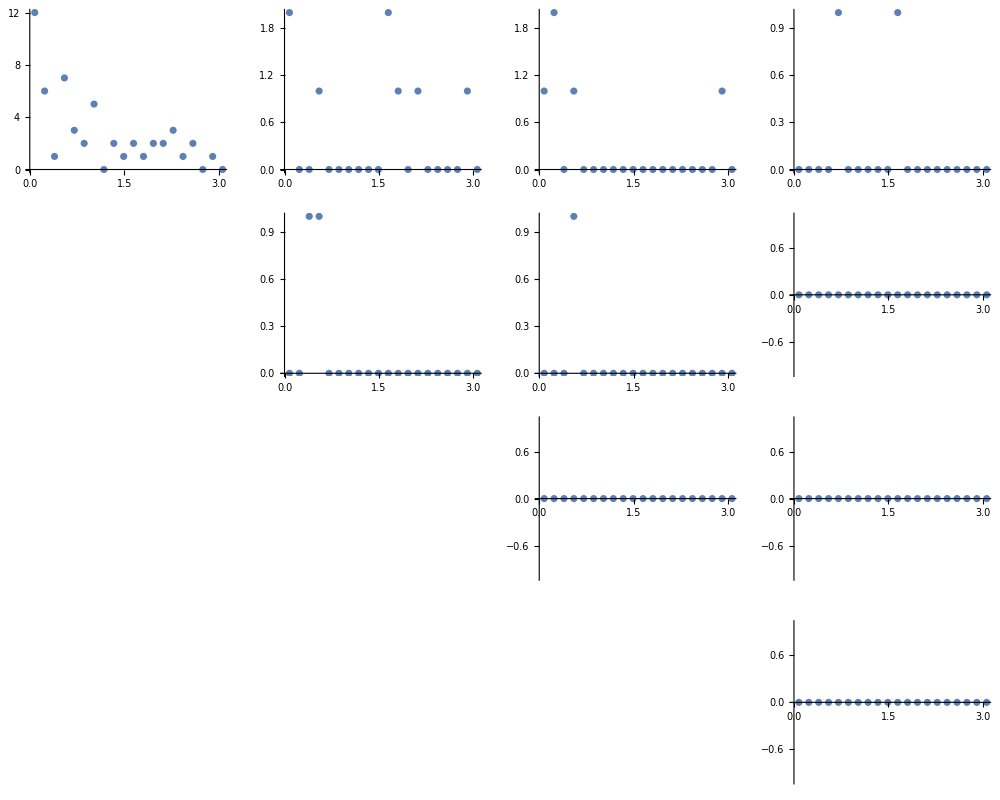

```mathematica
plots=ListPlot[#[[1]],
AxesLabel->MaTeX/@{"\\Delta\\phi","N"},
PlotLabel->MaTeX@#[[2]]
]&/@Transpose[{data,labels}];
grid=GraphicsGrid[{
{plots[[1]],plots[[2]],plots[[3]],plots[[4]]},
{Null,plots[[5]],plots[[6]],plots[[7]]},
{Null,Null,plots[[8]],plots[[9]]},
{Null,Null,Null,plots[[10]]}
},ItemAspectRatio->0.8,ImageSize->1000]
```

```mathematica
Export["STAR.pdf",grid];
```